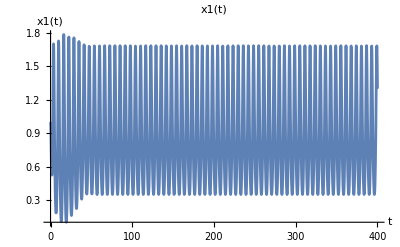

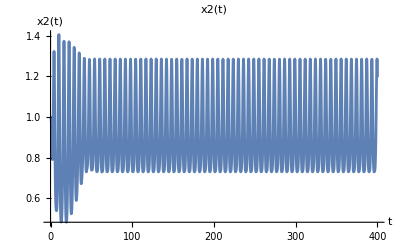

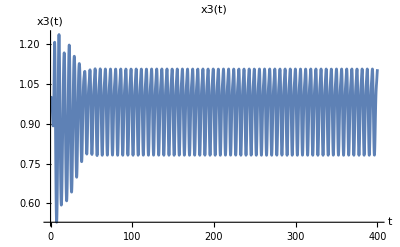

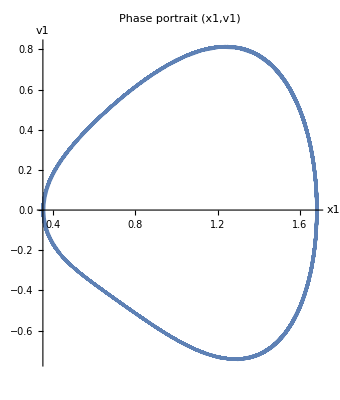

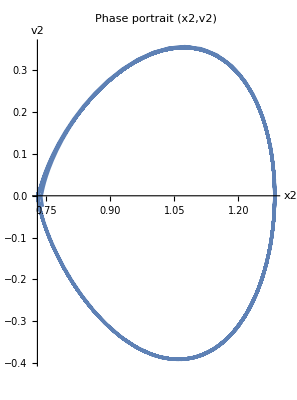

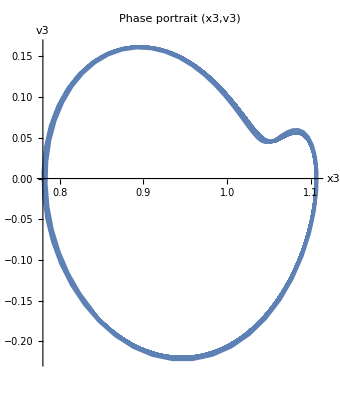

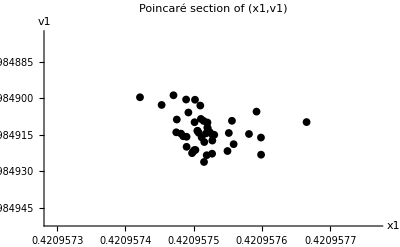

```mathematica
SetDirectory@NotebookDirectory[];

Clear[IntegrateAndPlot3DuffingParam];

(*三自由度 Duffing 链，带参数激励+外激励：x1''+c1 x1'+(a1+κ1 Cos[ωp t]) x1+b1 x1^3+kc (x1-x2)=F1 Cos[ω t] x2''+c2 x2'+(a2+κ2 Cos[ωp t]) x2+b2 x2^3+kc (2 x2-x1-x3)=F2 Cos[ω t] x3''+c3 x3'+(a3+κ3 Cos[ωp t]) x3+b3 x3^3+kc (x3-x2)=F3 Cos[ω t]-现在 κ 可以是一个标量（所有 DOF 用同一个幅值），也可以是长度为 3 的列表 {κ1,κ2,κ3}。-如果你想 F1=F2=F3=Ff，只要把 FVec 设成 {Ff,Ff,Ff} 即可。*)

IntegrateAndPlot3DuffingParam[aVec_:{-1.,-1.,-1.},(*{a1,a2,a3} 线性刚度*)bVec_:{1.,1.,1.},(*{b1,b2,b3} 立方非线性*)cVec_:{0.3,0.3,0.3},(*{c1,c2,c3} 阻尼*)kcVal_:1.,(*耦合刚度 kc*)kappaSpec_:{1.1,0,0},(*κ，可为标量或 {κ1,κ2,κ3}*)FVec_:{0.0,0.0,0.0},(*{F1,F2,F3} 外激励幅值*)omega_:1.,(*外激励频率 ω*)omegaP_:1.,(*参数激励频率 ωp*)tmax_:400.,dt_:0.001,ic_:Automatic,(*初值 {x1,x2,x3,v1,v2,v3}*)tSettle_:50.]:=Module[{a1,a2,a3,b1,b2,b3,c1,c2,c3,F1,F2,F3,kc,κ1,κ2,κ3,x10,x20,x30,v10,v20,v30,x1,x2,x3,v1,v2,v3,t,x1Fun,x2Fun,x3Fun,v1Fun,v2Fun,v3Fun,Tmain,tgrid,xPlot1,xPlot2,xPlot3,phase1,phase2,phase3,poincT0,nP,poincPts,poincPlot},{a1,a2,a3}=aVec;
{b1,b2,b3}=bVec;
{c1,c2,c3}=cVec;
{F1,F2,F3}=FVec;
kc=kcVal;
(*处理 κ：可以是标量，也可以是 {κ1,κ2,κ3}*)If[ListQ[kappaSpec],If[Length[kappaSpec]!=3,Print["❌ kappaSpec 必须是标量或长度为 3 的列表，例如 0.2 或 {0.2,0.1,0.05}。"];
Abort[];];
{κ1,κ2,κ3}=kappaSpec,(*标量情况：三个 DOF 用同一个 κ*)κ1=κ2=κ3=kappaSpec;];
{x10,x20,x30,v10,v20,v30}=If[ic===Automatic,{1.,1.,1.,0.,0.,0.},ic];
Tmain=2 Pi/omega;
Clear[x1,x2,x3,v1,v2,v3,t];
{x1Fun,x2Fun,x3Fun,v1Fun,v2Fun,v3Fun}=NDSolveValue[{x1'[t]==v1[t],x2'[t]==v2[t],x3'[t]==v3[t],(*DOF1：使用 κ1*)v1'[t]==-c1 v1[t]-(a1+κ1 Cos[omegaP t]) x1[t]-b1 x1[t]^3-kc (x1[t]-x2[t])+F1 Cos[omega t],(*DOF2：使用 κ2*)v2'[t]==-c2 v2[t]-(a2+κ2 Cos[omegaP t]) x2[t]-b2 x2[t]^3-kc (2 x2[t]-x1[t]-x3[t])+F2 Cos[omega t],(*DOF3：使用 κ3*)v3'[t]==-c3 v3[t]-(a3+κ3 Cos[omegaP t]) x3[t]-b3 x3[t]^3-kc (x3[t]-x2[t])+F3 Cos[omega t],(*⚠ 这里一定要用逗号分隔初值条件*)x1[0]==x10,x2[0]==x20,x3[0]==x30,v1[0]==v10,v2[0]==v20,v3[0]==v30},{x1,x2,x3,v1,v2,v3},{t,0,tmax}];
tgrid=N@Range[0,tmax,dt];
(*时间历程*)xPlot1=Plot[x1Fun[t],{t,0,tmax},AxesLabel->{"t","x1(t)"},PlotRange->All,PlotLabel->"x1(t)"];
xPlot2=Plot[x2Fun[t],{t,0,tmax},AxesLabel->{"t","x2(t)"},PlotRange->All,PlotLabel->"x2(t)"];
xPlot3=Plot[x3Fun[t],{t,0,tmax},AxesLabel->{"t","x3(t)"},PlotRange->All,PlotLabel->"x3(t)"];
(*相图（去掉过渡段）*)phase1=ParametricPlot[{x1Fun[t],v1Fun[t]},{t,tSettle,tmax},AxesLabel->{"x1","v1"},PlotRange->All,PlotLabel->"Phase portrait (x1,v1)"];
phase2=ParametricPlot[{x2Fun[t],v2Fun[t]},{t,tSettle,tmax},AxesLabel->{"x2","v2"},PlotRange->All,PlotLabel->"Phase portrait (x2,v2)"];
phase3=ParametricPlot[{x3Fun[t],v3Fun[t]},{t,tSettle,tmax},AxesLabel->{"x3","v3"},PlotRange->All,PlotLabel->"Phase portrait (x3,v3)"];
(*以主外激励周期做 Poincaré 截面（看 DOF1）*)poincT0=Max[tSettle,5 Tmain];
nP=Floor[(tmax-poincT0)/Tmain];
poincPts=Table[With[{tk=poincT0+k Tmain},{x1Fun[tk],v1Fun[tk]}],{k,0,nP}];
poincPlot=ListPlot[poincPts,PlotStyle->Black,PlotMarkers->{Automatic,8},AxesLabel->{"x1","v1"},PlotLabel->"Poincaré section of (x1,v1)"];
Print@xPlot1;
Print@xPlot2;
Print@xPlot3;
Print@phase1;
Print@phase2;
Print@phase3;
Print@poincPlot;];

(*示例：1) 原来统一幅值的情况（三个 DOF 都是 0.2）：IntegrateAndPlot3DuffingParam[kappaSpec->0.2];
2) 自定义三个 DOF 的参数扰动幅值：κ1=0.2,κ2=0.1,κ3=0.05 IntegrateAndPlot3DuffingParam[kappaSpec->{0.2,0.1,0.05}];*)

IntegrateAndPlot3DuffingParam[]
```

```mathematica
ClearAll[FRFSweep3,PlotFRF3];

FRFSweep3[a_:-1.,(*线性刚度 α*)b_:1.,(*非线性刚度 β*)c_:0.3,(*阻尼 c*)kc_:1.,(*耦合刚度 kc*)kappa_:0.0,(*参数激励幅值 κ*)F_:0.2,(*外激励幅值 F*)omegaMin_:0.5,(*扫频下限 Ω_min*)omegaMax_:1.5,(*扫频上限 Ω_max*)domega_:0.02,(*步长 ΔΩ*)omegaP_:1.       (*参数激励频率 Ω_p*)]:=Module[{cyclesSettle=60,cyclesMeasure=20,dt=0.001,ic0=ConstantArray[0.,6],(*{x1,x2,x3,v1,v2,v3}*)forwardGrid,backwardGrid,doOne,state,res,forward,backward},(*单个频率点：同时算出 x1,x2,x3 的 Amp*)doOne[omega_,{x10_,x20_,x30_,v10_,v20_,v30_}]:=Module[{T=2 Pi/omega,tS,tM,x1,x2,x3,v1,v2,v3,t,x1Fun,x2Fun,x3Fun,v1Fun,v2Fun,v3Fun,ts,xs1,xs2,xs3,xmax1,xmin1,amp1,xmax2,xmin2,amp2,xmax3,xmin3,amp3,lastState},tS=cyclesSettle*T;
tM=cyclesMeasure*T;
Clear[x1,x2,x3,v1,v2,v3,t];
{x1Fun,x2Fun,x3Fun,v1Fun,v2Fun,v3Fun}=NDSolveValue[{x1'[t]==v1[t],x2'[t]==v2[t],x3'[t]==v3[t],v1'[t]==-c v1[t]-(a+kappa Cos[omegaP t]) x1[t]-b x1[t]^3-kc (x1[t]-x2[t])+F Cos[omega t],v2'[t]==-c v2[t]-(a+kappa Cos[omegaP t]) x2[t]-b x2[t]^3-kc (2 x2[t]-x1[t]-x3[t])+F Cos[omega t],v3'[t]==-c v3[t]-(a+kappa Cos[omegaP t]) x3[t]-b x3[t]^3-kc (x3[t]-x2[t])+F Cos[omega t],x1[0]==x10,x2[0]==x20,x3[0]==x30,v1[0]==v10,v2[0]==v20,v3[0]==v30},{x1,x2,x3,v1,v2,v3},{t,0,tS+tM},Method->"ExplicitRungeKutta",MaxStepFraction->0.1];
ts=Range[tS,tS+tM,dt];
xs1=x1Fun/@ts;
xs2=x2Fun/@ts;
xs3=x3Fun/@ts;
xmax1=Max[xs1];xmin1=Min[xs1];amp1=(xmax1-xmin1)/2.;
xmax2=Max[xs2];xmin2=Min[xs2];amp2=(xmax2-xmin2)/2.;
xmax3=Max[xs3];xmin3=Min[xs3];amp3=(xmax3-xmin3)/2.;
lastState={x1Fun[tS+tM],x2Fun[tS+tM],x3Fun[tS+tM],v1Fun[tS+tM],v2Fun[tS+tM],v3Fun[tS+tM]};
<|"Omega"->omega,"Amp1"->amp1,"Amp2"->amp2,"Amp3"->amp3,"xend"->lastState|>];
(*前扫*)forwardGrid=Range[omegaMin,omegaMax,domega];
state=ic0;
forward=Table[res=doOne[omega,state];
state=res["xend"];
KeyDrop[res,"xend"],{omega,forwardGrid}];
(*后扫*)backwardGrid=Range[omegaMax,omegaMin,-domega];
state=ic0;
res=doOne[omegaMax,state];
state=res["xend"];
backward=Table[res=doOne[omega,state];
state=res["xend"];
KeyDrop[res,"xend"],{omega,backwardGrid}];
<|"forward"->forward,"backward"->backward,"params"-><|"a"->a,"b"->b,"c"->c,"kc"->kc,"kappa"->kappa,"F"->F,"omegaP"->omegaP,"omegaMin"->omegaMin,"omegaMax"->omegaMax,"domega"->domega|>|>];
PlotFRF3[frf_Association]:=Module[{dataF1,dataB1,dataF2,dataB2,dataF3,dataB3,params,plot1,plot2,plot3},params=frf["params"];
dataF1=Values/@(frf["forward"][[All,{"Omega","Amp1"}]]);
dataB1=Values/@(frf["backward"][[All,{"Omega","Amp1"}]]);
dataF2=Values/@(frf["forward"][[All,{"Omega","Amp2"}]]);
dataB2=Values/@(frf["backward"][[All,{"Omega","Amp2"}]]);
dataF3=Values/@(frf["forward"][[All,{"Omega","Amp3"}]]);
dataB3=Values/@(frf["backward"][[All,{"Omega","Amp3"}]]);
plot1=ListLinePlot[{dataF1,dataB1},PlotLegends->{"前扫","后扫"},PlotMarkers->{Automatic,5},AxesLabel->{"Ω","Amp(x1)"},PlotLabel->"FRF of x1",PlotRange->All];
plot2=ListLinePlot[{dataF2,dataB2},PlotLegends->{"前扫","后扫"},PlotMarkers->{Automatic,5},AxesLabel->{"Ω","Amp(x2)"},PlotLabel->"FRF of x2",PlotRange->All];
plot3=ListLinePlot[{dataF3,dataB3},PlotLegends->{"前扫","后扫"},PlotMarkers->{Automatic,5},AxesLabel->{"Ω","Amp(x3)"},PlotLabel->"FRF of x3",PlotRange->All];
GraphicsGrid[{{plot1,plot2,plot3}},ImageSize->Large,PlotLabel->Row[{"3DOF Duffing FRF   ","a=",params["a"],", b=",params["b"],", c=",params["c"],", kc=",params["kc"],", κ=",params["kappa"],", Ωp=",params["omegaP"],", F=",params["F"]}]]];
frf3=FRFSweep3[];    (*扫频，算出 x1,x2,x3 的 FRF*)
PlotFRF3[frf3]       (*一次性画出三自由度的 FRF 图*)
```

-Graphics-

```mathematica
ClearAll[ParamSweep3,PlotParamSweep3];

ParamSweep3[a_:-1.,(*线性刚度 α*)b_:1.,(*非线性刚度 β*)c_:0.3,(*阻尼 c*)kc_:1.,(*耦合刚度 kc*)kappa_:0.3,(*参数激励幅值 κ，稍微调大一点更容易看到效应*)F_:0.0,(*外激励幅值 F，适当减小一点*)omega_:1.,(*外激励频率 Ω_f，固定*)omegaPMin_:0.5,(*参数激励扫频下限 Ωp_min*)omegaPMax_:1.5,(*参数激励扫频上限 Ωp_max*)domegaP_:0.02    (*参数激励频率步长 ΔΩp*)]:=Module[{cyclesSettle=60,cyclesMeasure=20,dt=0.001,ic0=ConstantArray[0.1,6],(*{x1,x2,x3,v1,v2,v3}*)forwardGrid,backwardGrid,doOne,state,res,forward,backward},doOne[omegaPcur_,{x10_,x20_,x30_,v10_,v20_,v30_}]:=Module[{(*☆关键修改：按参数激励周期 Tp 来计时*)Tp=2 Pi/omegaPcur,tS,tM,x1,x2,x3,v1,v2,v3,t,x1Fun,x2Fun,x3Fun,v1Fun,v2Fun,v3Fun,ts,xs1,xs2,xs3,xmax1,xmin1,amp1,xmax2,xmin2,amp2,xmax3,xmin3,amp3,lastState},tS=cyclesSettle*Tp;
tM=cyclesMeasure*Tp;
Clear[x1,x2,x3,v1,v2,v3,t];
{x1Fun,x2Fun,x3Fun,v1Fun,v2Fun,v3Fun}=NDSolveValue[{x1'[t]==v1[t],x2'[t]==v2[t],x3'[t]==v3[t],v1'[t]==-c v1[t]-(a+kappa Cos[omegaPcur t]) x1[t]-b x1[t]^3-kc (x1[t]-x2[t])+F Cos[omega t],v2'[t]==-c v2[t]-(a+kappa Cos[omegaPcur t]) x2[t]-b x2[t]^3-kc (2 x2[t]-x1[t]-x3[t])+F Cos[omega t],v3'[t]==-c v3[t]-(a+kappa Cos[omegaPcur t]) x3[t]-b x3[t]^3-kc (x3[t]-x2[t])+F Cos[omega t],x1[0]==x10,x2[0]==x20,x3[0]==x30,v1[0]==v10,v2[0]==v20,v3[0]==v30},{x1,x2,x3,v1,v2,v3},{t,0,tS+tM},Method->"ExplicitRungeKutta",MaxStepFraction->0.1];
ts=Range[tS,tS+tM,dt];
xs1=x1Fun/@ts;
xs2=x2Fun/@ts;
xs3=x3Fun/@ts;
xmax1=Max[xs1];xmin1=Min[xs1];amp1=(xmax1-xmin1)/2.;
xmax2=Max[xs2];xmin2=Min[xs2];amp2=(xmax2-xmin2)/2.;
xmax3=Max[xs3];xmin3=Min[xs3];amp3=(xmax3-xmin3)/2.;
lastState={x1Fun[tS+tM],x2Fun[tS+tM],x3Fun[tS+tM],v1Fun[tS+tM],v2Fun[tS+tM],v3Fun[tS+tM]};
<|"OmegaP"->omegaPcur,"Amp1"->amp1,"Amp2"->amp2,"Amp3"->amp3,"xend"->lastState|>];
(*前扫& 后扫 完全照旧*)forwardGrid=Range[omegaPMin,omegaPMax,domegaP];
state=ic0;
forward=Table[res=doOne[omegaPcur,state];
state=res["xend"];
KeyDrop[res,"xend"],{omegaPcur,forwardGrid}];
backwardGrid=Range[omegaPMax,omegaPMin,-domegaP];
state=ic0;
res=doOne[omegaPMax,state];
state=res["xend"];
backward=Table[res=doOne[omegaPcur,state];
state=res["xend"];
KeyDrop[res,"xend"],{omegaPcur,backwardGrid}];
<|"forward"->forward,"backward"->backward,"params"-><|"a"->a,"b"->b,"c"->c,"kc"->kc,"kappa"->kappa,"F"->F,"omega"->omega,"omegaPMin"->omegaPMin,"omegaPMax"->omegaPMax,"domegaP"->domegaP|>|>];

PlotParamSweep3[frf_Association]:=Module[{dataF1,dataB1,dataF2,dataB2,dataF3,dataB3,params,plot1,plot2,plot3},params=frf["params"];
dataF1=Values/@(frf["forward"][[All,{"OmegaP","Amp1"}]]);
dataB1=Values/@(frf["backward"][[All,{"OmegaP","Amp1"}]]);
dataF2=Values/@(frf["forward"][[All,{"OmegaP","Amp2"}]]);
dataB2=Values/@(frf["backward"][[All,{"OmegaP","Amp2"}]]);
dataF3=Values/@(frf["forward"][[All,{"OmegaP","Amp3"}]]);
dataB3=Values/@(frf["backward"][[All,{"OmegaP","Amp3"}]]);
plot1=ListLinePlot[{dataF1,dataB1},PlotLegends->{"前扫","后扫"},PlotMarkers->{Automatic,5},AxesLabel->{"Ω_p","Amp(x1)"},PlotLabel->"参数激励 FRF of x1",PlotRange->All];
plot2=ListLinePlot[{dataF2,dataB2},PlotLegends->{"前扫","后扫"},PlotMarkers->{Automatic,5},AxesLabel->{"Ω_p","Amp(x2)"},PlotLabel->"参数激励 FRF of x2",PlotRange->All];
plot3=ListLinePlot[{dataF3,dataB3},PlotLegends->{"前扫","后扫"},PlotMarkers->{Automatic,5},AxesLabel->{"Ω_p","Amp(x3)"},PlotLabel->"参数激励 FRF of x3",PlotRange->All];
GraphicsGrid[{{plot1,plot2,plot3}},ImageSize->Large,PlotLabel->Row[{"3DOF Duffing 参数激励扫频  ","a=",params["a"],", b=",params["b"],", c=",params["c"],", kc=",params["kc"],", κ=",params["kappa"],", Ω_f=",params["omega"],", F=",params["F"]}]]];
paramFrf=ParamSweep3[];
PlotParamSweep3[paramFrf]
```

-Graphics-

数据生成配置：

方程: 3DOF：仅 x1 含 (α + κ cos(Ω t))，x2、x3 为 α 线性刚度 + 非线性 + 耦合

参数激励 Ω: 21 点 [0.500 ~ 1.500 rad/s]

幅值 κ: 10 点 {0,0.5,1,1.1,1.2,1.3,1.4,1.5,2,3}

总组合: 210

静平衡: xₛ ∈ {-1.00, 1.00}

进度: 20/210

进度: 40/210

进度: 60/210

进度: 80/210

进度: 100/210

进度: 120/210

进度: 140/210

进度: 160/210

进度: 180/210

进度: 200/210

进度: 210/210

数据抽样完成：

训练集: 1344084 样本

验证集: 336000 样本

测试集: 336000 样本

统计信息：

输入 [x1,x2,x3,v1,v2,v3,κ_eff]: μ = {-0.00,-0.00,-0.00,0.00,0.00,-0.00,-0.00}, σ = {0.99,0.92,0.93,0.61,0.41,0.43,1.07}

输出 [ga1,ga2,ga3]: μ = {-0.000,0.000,0.000}, σ = {1.002,0.569,0.558}

✅ 数据已保存

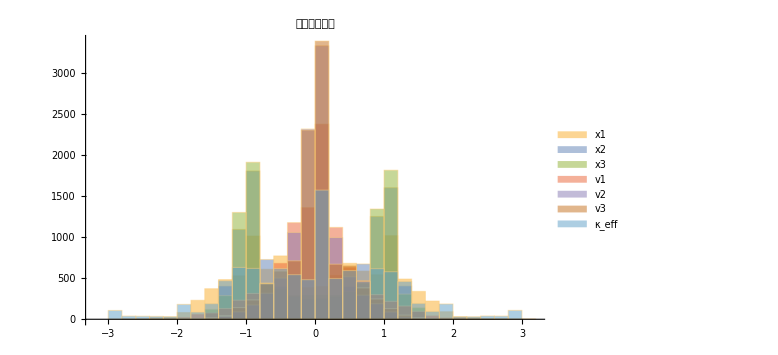

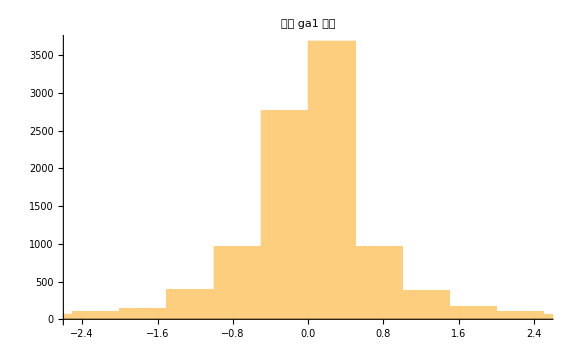

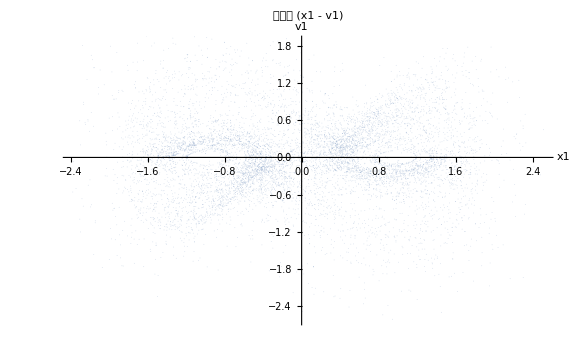

✅ 完成

```mathematica
SetDirectory@NotebookDirectory[];

ClearAll[α,β,c,kc,FindStableEq,GenerateDataFromInitial3Param,freqList,kappaList,allTrainData,allValData,allTestData,trainData,valData,testData,allInputs,allTargets,inputMean,inputStd,targetMeanGa,targetStdGa];

(*----------物理参数（双稳+耦合）----------*)
α=-1.;
β=1.;
c=0.3;
kc=1.;   (*耦合刚度，可按需改*)

(*----------计算两个稳定静平衡（单自由度）----------*)
FindStableEq[α_,β_]:=Module[{xs},xs=x/. NSolve[β x^3+α x==0,x,Reals];
Sort@Select[xs,(α+3 β #^2)>0&]];

stables=FindStableEq[α,β];
If[Length[stables]<2,Print["❌ 未找到两个稳定平衡，请检查参数。"];
Abort[];];

orix1=stables[[1]];
orix2=stables[[2]];

(*==================================================*)
(*从一个 3DOF 初值生成数据（只对第 1 个自由度施加参数激励+耦合）*)
(*==================================================*)
(*方程：x1''+c x1'+(α+κ cos(Ω t)) x1+β x1^3+kc (x1-x2)=0 x2''+c x2'+α x2+β x2^3+kc (2 x2-x1-x3)=0 x3''+c x3'+α x3+β x3^3+kc (x3-x2)=0 输入:{x1,x2,x3,v1,v2,v3,κ_eff} 其中 κ_eff(t)=κ cos(Ω t) 输出:{ga1,ga2,ga3}*)

GenerateDataFromInitial3Param[freq_,kappa_,orixVec_List]:=Module[{Ω,tEnd,h,tgrid,x1Fun,x2Fun,x3Fun,v1Fun,v2Fun,v3Fun,x1vals,x2vals,x3vals,v1vals,v2vals,v3vals,kappaEffVals,(*κ_eff(t)=κ cos(Ω t)*)dataList},Ω=2 Pi freq;(*参数激励圆频率*)tEnd=100./freq;(*模拟约 100 个参数周期*)h=1./(200. freq);(*每周期约 200 个点*)tgrid=N@Range[0,tEnd,h];
Clear[x1,x2,x3,v1,v2,v3,t];
{x1Fun,x2Fun,x3Fun,v1Fun,v2Fun,v3Fun}=NDSolveValue[{x1'[t]==v1[t],x2'[t]==v2[t],x3'[t]==v3[t],(*只对第一个自由度施加参数激励*)v1'[t]==-c v1[t]-(α+kappa Cos[Ω t]) x1[t]-β x1[t]^3-kc (x1[t]-x2[t]),(*第二、第三自由度无参数激励，仅含 α 线性刚度*)v2'[t]==-c v2[t]-α x2[t]-β x2[t]^3-kc (2 x2[t]-x1[t]-x3[t]),v3'[t]==-c v3[t]-α x3[t]-β x3[t]^3-kc (x3[t]-x2[t]),x1[0]==orixVec[[1]],x2[0]==orixVec[[2]],x3[0]==orixVec[[3]],v1[0]==0.,v2[0]==0.,v3[0]==0.},{x1,x2,x3,v1,v2,v3},{t,0,tEnd},MaxStepSize->h/2];
x1vals=x1Fun/@tgrid;
x2vals=x2Fun/@tgrid;
x3vals=x3Fun/@tgrid;
v1vals=v1Fun/@tgrid;
v2vals=v2Fun/@tgrid;
v3vals=v3Fun/@tgrid;
(*参数激励瞬时值 κ_eff(t)*)kappaEffVals=kappa Cos[Ω tgrid];
dataList=Table[Module[{x1v=x1vals[[i]],x2v=x2vals[[i]],x3v=x3vals[[i]],v1v=v1vals[[i]],v2v=v2vals[[i]],v3v=v3vals[[i]],κeff=kappaEffVals[[i]],ga1,ga2,ga3,input},(*对应方程的瞬时加速度（只有 ga1 中含参数激励）*)ga1=-c v1v-(α+κeff) x1v-β x1v^3-kc (x1v-x2v);
ga2=-c v2v-α x2v-β x2v^3-kc (2 x2v-x1v-x3v);
ga3=-c v3v-α x3v-β x3v^3-kc (x3v-x2v);
(*输入特征*)input={x1v,x2v,x3v,v1v,v2v,v3v,κeff};
input->{ga1,ga2,ga3}],{i,Length[tgrid]}];
dataList];

(* ==================分层采样配置==================*)
freqList=Range[0.5,1.5,0.05]/(2 Pi);
(*和你原来的写法一致：Ω∈[0.5,1.5] rad/s*)

kappaList={0,0.5,1,1.1,1.2,1.3,1.4,1.5,2,3};

Print["数据生成配置："];
Print["  方程: 3DOF：仅 x1 含 (α + κ cos(Ω t))，x2、x3 为 α 线性刚度 + 非线性 + 耦合"];
Print["  参数激励 Ω: ",Length[freqList]," 点 [",NumberForm[freqList[[1]]*2*Pi,{4,3}]," ~ ",NumberForm[freqList[[-1]]*2*Pi,{4,3}]," rad/s]"];
Print["  幅值 κ: ",Length[kappaList]," 点 ",kappaList];
Print["  总组合: ",Length[freqList]*Length[kappaList]];
Print["  静平衡: xₛ ∈ {",NumberForm[orix1,{4,2}],", ",NumberForm[orix2,{4,2}],"}"];

allTrainData={};
allValData={};
allTestData={};

totalCombinations=Length[freqList]*Length[kappaList];
currentCombination=0;

Do[Do[Module[{samples1,samples2,allSamplesCombo,shuffled,splitIdx,icA,icB},currentCombination++;
If[Mod[currentCombination,20]==0||currentCombination==totalCombinations,Print["  进度: ",currentCombination,"/",totalCombinations];];
(*三个自由度分别从左井/右井出发*)icA={orix1,orix1,orix1};
icB={orix2,orix2,orix2};
samples1=GenerateDataFromInitial3Param[freq,kappa,icA];
samples2=GenerateDataFromInitial3Param[freq,kappa,icB];
allSamplesCombo=Join[samples1,samples2];
shuffled=RandomSample[allSamplesCombo];
splitIdx=Round[0.8*Length[shuffled]];
allTrainData=Join[allTrainData,shuffled[[1;;splitIdx]]];
allValData=Join[allValData,shuffled[[splitIdx+1;;-1]]];],{kappa,kappaList}],{freq,freqList}];

allTrainData=RandomSample[allTrainData];
allValData=RandomSample[allValData];

(* ==================随机抽取 20%==================*)
samplingRatio=0.2;
trainSize=Round[Length[allTrainData]*samplingRatio];
valSize=Round[Length[allValData]*samplingRatio];
testSize=Round[Length[allValData]*samplingRatio];

trainData=RandomSample[allTrainData,trainSize];
valData=RandomSample[allValData,valSize];
testData=RandomSample[allValData,testSize];

Print["数据抽样完成："];
Print["  训练集: ",Length[trainData]," 样本"];
Print["  验证集: ",Length[valData]," 样本"];
Print["  测试集: ",Length[testData]," 样本"];

(* ==================数据统计==================*)
allInputs=trainData[[All,1]];   (*7 维输入*)
allTargets=trainData[[All,2]];   (*3 维输出*)

inputMean=Mean[allInputs];
inputStd=StandardDeviation[allInputs];

targetMeanGa=Mean[allTargets];
targetStdGa=StandardDeviation[allTargets];

Print["统计信息："];
Print["  输入 [x1,x2,x3,v1,v2,v3,κ_eff]: μ = ",NumberForm[inputMean,{4,2}],", σ = ",NumberForm[inputStd,{4,2}]];
Print["  输出 [ga1,ga2,ga3]: μ = ",NumberForm[targetMeanGa,{6,3}],", σ = ",NumberForm[targetStdGa,{6,3}]];

(* ==================保存数据==================*)
Export[FileNameJoin[{Directory[],"trainData_3dof_parametric_duffing.mx"}],trainData,"MX"];
Export[FileNameJoin[{Directory[],"valData_3dof_parametric_duffing.mx"}],valData,"MX"];
Export[FileNameJoin[{Directory[],"testData_3dof_parametric_duffing.mx"}],testData,"MX"];

normParams=<|"inputMean"->inputMean,"inputStd"->inputStd,"targetMeanGa"->targetMeanGa,"targetStdGa"->targetStdGa,"freqList"->freqList,"kappaList"->kappaList,"alpha"->α,"beta"->β,"damping"->c,"kc"->kc|>;

Export[FileNameJoin[{Directory[],"normParams_3dof_parametric_duffing.mx"}],normParams,"MX"];

Print["✅ 数据已保存"];

(* ==================简单可视化==================*)
sampleSize=Min[10000,Length[trainData]];
sampledData=RandomSample[trainData,sampleSize];
sampledInputs=sampledData[[All,1]];
sampledTargets=sampledData[[All,2]];

fig1=Histogram[Transpose[sampledInputs],30,PlotLabel->"输入特征分布",ChartLegends->{"x1","x2","x3","v1","v2","v3","κ_eff"},ImageSize->Large];

fig2=Histogram[sampledTargets[[All,1]],50,(*先看 ga1 的分布*)PlotLabel->"输出 ga1 分布",ImageSize->Large];

fig3=ListPlot[sampledInputs[[All,{1,4}]],(*x1-v1 相图*)PlotStyle->{PointSize[0.001],Opacity[0.3]},AxesLabel->{"x1","v1"},PlotLabel->"相空间 (x1 - v1)",ImageSize->Large];

Print@fig1;
Print@fig2;
Print@fig3;

Print["✅ 完成"];
```

```mathematica
(* ==================神经网络训练：3DOF 参数激励 Duffing 系统==================*)(*输入:[x1,x2,x3,v1,v2,v3,κ_eff(t)]*)(*输出:[ga1,ga2,ga3]=三个自由度的瞬时加速度*)SetDirectory@NotebookDirectory[];

ClearAll[MyNormalize,EvaluateOnDataset,ExportToExcel];

(*-------------------1. 加载数据-------------------*)

trainData=Import["trainData_3dof_parametric_duffing.mx"];
valData=Import["valData_3dof_parametric_duffing.mx"];
testData=Import["testData_3dof_parametric_duffing.mx"];

Print["数据加载完成："];
Print["  训练集: ",Length[trainData]," 样本"];
Print["  验证集: ",Length[valData]," 样本"];
Print["  测试集: ",Length[testData]," 样本"];
Print["  总计: ",Length[trainData]+Length[valData]+Length[testData]," 样本"];

(*归一化函数*)
MyNormalize[x_,m_,s_]:=(x-m)/s;

(*提取输入/目标*)
allInputs=trainData[[All,1]];
allTargets=trainData[[All,2]];

inDim=Length[allInputs[[1]]];
outDim=Length[allTargets[[1]]];

Print["输入维度: ",inDim,", 输出维度: ",outDim];

(*-------------------2. 统计与标准化-------------------*)

inputMean=Mean[allInputs];
inputStd=StandardDeviation[allInputs]+10^-10;

targetMean=Mean[allTargets];          (*向量 {μ_ga1,μ_ga2,μ_ga3}*)
targetStd=StandardDeviation[allTargets]+10^-10;

trainDataNorm=Table[MyNormalize[trainData[[i,1]],inputMean,inputStd]->MyNormalize[trainData[[i,2]],targetMean,targetStd],{i,Length[trainData]}];

valDataNorm=Table[MyNormalize[valData[[i,1]],inputMean,inputStd]->MyNormalize[valData[[i,2]],targetMean,targetStd],{i,Length[valData]}];

testDataNorm=Table[MyNormalize[testData[[i,1]],inputMean,inputStd]->MyNormalize[testData[[i,2]],targetMean,targetStd],{i,Length[testData]}];

(*-------------------3. 网络架构-------------------*)

net=NetChain[{LinearLayer[128],Tanh,LinearLayer[64],Tanh,LinearLayer[outDim]},"Input"->inDim,"Output"->outDim];

(*-------------------4. 通用评估函数-------------------*)

EvaluateOnDataset[nn_,dataset_,datasetName_String]:=Module[{inputsNorm,predNorm,pred,true,rmseVec,stdTrueVec,relErrVec,score},inputsNorm=Map[MyNormalize[#,inputMean,inputStd]&,dataset[[All,1]]];
predNorm=nn[inputsNorm];
(*反归一化到物理量*)pred=Map[#*targetStd+targetMean&,predNorm];
true=dataset[[All,2]];
rmseVec=Sqrt@Mean[(pred-true)^2];(*3 维 RMSE*)stdTrueVec=StandardDeviation/@Transpose[true];
relErrVec=100 rmseVec/stdTrueVec;(*相对误差%*)score=Mean[rmseVec];(*平均 RMSE*)Print["\n",datasetName,"评估："];
Print["  RMSE = ",NumberForm[rmseVec,{6,4}]];
Print["  Rel% = ",NumberForm[relErrVec,{5,2}]];
Print["  Score = ",NumberForm[score,{6,4}]];
<|"rmse"->rmseVec,"rel%"->relErrVec,"score"->score,"pred"->pred,"true"->true,"datasetName"->datasetName|>];

(*-------------------5. 多阶段训练-------------------*)

stages={<|"rounds"->2000,"lr"->0.0005|>,<|"rounds"->3000,"lr"->0.0001|>,<|"rounds"->3000,"lr"->0.00005|>,<|"rounds"->2000,"lr"->0.00001|>};

Print["\n开始多阶段训练..."];

bestNet=net;
bestStats=<|"score"->Infinity|>;
currNet=net;

Do[Print["\n========== Stage ",si," : rounds=",stages[[si,"rounds"]],", lr=",stages[[si,"lr"]]," =========="];
tr=NetTrain[currNet,trainDataNorm,All,ValidationSet->valDataNorm,MaxTrainingRounds->stages[[si,"rounds"]],BatchSize->1024,LearningRate->stages[[si,"lr"]],Method->{"ADAM"},TargetDevice->"CPU",TrainingProgressReporting->"Panel"];
currNet=tr["TrainedNet"];
stats=EvaluateOnDataset[currNet,valData,"验证集"];
If[stats["score"]<bestStats["score"],bestNet=currNet;
bestStats=stats;
Export["checkpoint_best_stage"<>ToString[si]<>"_3dof_param.wlnet",bestNet,"WLNet"];
Print["✅ 更新最佳模型已保存 (Stage ",si,")"];];,{si,Length[stages]}];

trainedNet=bestNet;

(*-------------------6. 保存模型与归一化参数-------------------*)

normParams=<|"inputMean"->inputMean,"inputStd"->inputStd,"targetMean"->targetMean,"targetStd"->targetStd|>;

Export["normParams_3dof_parametric_final.mx",normParams,"MX"];
Export["trainedNet_3dof_parametric_final.wlnet",trainedNet,"WLNet"];
Print["\n✅ 模型与归一化参数已保存"];

(*-------------------7. 评估所有数据集-------------------*)

Print["\n========================================"];
Print["最终评估："];
Print["========================================"];

trainResults=EvaluateOnDataset[trainedNet,trainData,"训练集"];
valResults=EvaluateOnDataset[trainedNet,valData,"验证集"];
testResults=EvaluateOnDataset[trainedNet,testData,"测试集"];

allData=Join[trainData,valData,testData];
allResults=EvaluateOnDataset[trainedNet,allData,"总集(全部数据)"];

(*-------------------8. Excel 导出（先对 DOF1，其他类似改 All,2/3 即可）-------------------*)

ExportToExcel[yTrue_,yPred_,errors_,filename_,sheetName_,maxRows_:10000]:=Module[{headers,dataRows,outputData,sampleIndices,actualTrue,actualPred,actualErrors},If[Length[yTrue]>maxRows,Print["⚠ ",sheetName,"数据量(",Length[yTrue],")超过限制，随机采样",maxRows,"行"];
sampleIndices=RandomSample[Range[Length[yTrue]],maxRows];
actualTrue=yTrue[[sampleIndices]];
actualPred=yPred[[sampleIndices]];
actualErrors=errors[[sampleIndices]],actualTrue=yTrue;
actualPred=yPred;
actualErrors=errors];
headers={"真实 ga1","预测 ga1","误差","绝对误差","相对误差(%)"};
dataRows=Table[{actualTrue[[i]],actualPred[[i]],actualErrors[[i]],Abs[actualErrors[[i]]],If[Abs[actualTrue[[i]]]>10^-10,100*Abs[actualErrors[[i]]]/Abs[actualTrue[[i]]],0]},{i,Length[actualTrue]}];
outputData=Join[{headers},dataRows];
Export[filename,outputData,"XLSX"];
Print["✅ ",sheetName,"数据已导出到: ",filename];
Print["   实际导出行数: ",Length[dataRows]," (不含表头)"];];

Print["\n========================================"];
Print["导出Excel文件（限制每个数据集最多10000行，当前只导 ga1）："];
Print["========================================"];

maxRowsPerSheet=10000;

(*从结果中取出 DOF1 (ga1)，其他 DOF2/3 换成[[All,2]]/[[All,3]] 即可*)
trainTrue=trainResults["true"][[All,2]];
trainPred=trainResults["pred"][[All,2]];
trainErrors=trainPred-trainTrue;

valTrue=valResults["true"][[All,2]];
valPred=valResults["pred"][[All,2]];
valErrors=valPred-valTrue;

testTrue=testResults["true"][[All,2]];
testPred=testResults["pred"][[All,2]];
testErrors=testPred-testTrue;

allTrue=allResults["true"][[All,2]];
allPred=allResults["pred"][[All,2]];
allErrors=allPred-allTrue;

ExportToExcel[trainTrue,trainPred,trainErrors,"training_results_3dof_ga1.xlsx","训练集",maxRowsPerSheet];

ExportToExcel[valTrue,valPred,valErrors,"validation_results_3dof_ga1.xlsx","验证集",maxRowsPerSheet];

ExportToExcel[testTrue,testPred,testErrors,"test_results_3dof_ga1.xlsx","测试集",maxRowsPerSheet];

ExportToExcel[allTrue,allPred,allErrors,"all_results_3dof_ga1.xlsx","总集",maxRowsPerSheet];

(*-------------------9. 回归图-------------------*)

CreateRegressionPlot[yTrue_,yPred_,title_,relErr_]:=Module[{ymin,ymax,sampleIndices,ySample,pSample},If[Length[yTrue]>2000,sampleIndices=RandomSample[Range[Length[yTrue]],2000];
ySample=yTrue[[sampleIndices]];
pSample=yPred[[sampleIndices]],ySample=yTrue;
pSample=yPred];
ymin=Min[yTrue];
ymax=Max[yTrue];
ListPlot[Transpose[{ySample,pSample}],PlotStyle->{Blue,PointSize[0.005],Opacity[0.5]},PlotLabel->Row[{title," (相对误差: ",NumberForm[relErr,{5,2}],"%, DOF1)"}],AxesLabel->{"真实 ga1","预测 ga1"},AspectRatio->1,ImageSize->Medium,Epilog->{Red,Dashed,Line[{{ymin,ymin},{ymax,ymax}}]}]];

Print["\n绘制回归图 (ga1)："];

trainPlot=CreateRegressionPlot[trainTrue,trainPred,"训练集",trainResults["rel%"][[1]]];
valPlot=CreateRegressionPlot[valTrue,valPred,"验证集",valResults["rel%"][[1]]];
testPlot=CreateRegressionPlot[testTrue,testPred,"测试集",testResults["rel%"][[1]]];
allPlot=CreateRegressionPlot[allTrue,allPred,"总集",allResults["rel%"][[1]]];

GraphicsGrid[{{trainPlot,valPlot},{testPlot,allPlot}},ImageSize->Large];

(*-------------------10. 误差分布-------------------*)

CreateErrorHist[errors_,title_]:=Histogram[errors,50,PlotLabel->title<>" 误差分布 (ga1)",AxesLabel->{"误差","频数"},ImageSize->Medium];

Print["\n绘制误差分布 (ga1)："];

trainErrorHist=CreateErrorHist[trainErrors,"训练集"];
valErrorHist=CreateErrorHist[valErrors,"验证集"];
testErrorHist=CreateErrorHist[testErrors,"测试集"];
allErrorHist=CreateErrorHist[allErrors,"总集"];

GraphicsGrid[{{trainErrorHist,valErrorHist},{testErrorHist,allErrorHist}},ImageSize->Large];

(*-------------------11. 统计摘要-------------------*)

Print["\n========================================"];
Print["统计摘要（ga1）："];
Print["========================================"];

PrintStats[results_,name_]:=Module[{errors,maxErr,meanErr,medianErr},errors=Abs[results["pred"][[All,1]]-results["true"][[All,1]]];
maxErr=Max[errors];
meanErr=Mean[errors];
medianErr=Median[errors];
Print[name,":"];
Print["  样本数: ",Length[errors]];
Print["  RMSE: ",NumberForm[results["rmse"][[1]],{6,4}]];
Print["  相对误差: ",NumberForm[results["rel%"][[1]],{5,2}],"%"];
Print["  最大误差: ",NumberForm[maxErr,{6,4}]];
Print["  平均误差: ",NumberForm[meanErr,{6,4}]];
Print["  中位误差: ",NumberForm[medianErr,{6,4}]];];

PrintStats[trainResults,"训练集"];
PrintStats[valResults,"验证集"];
PrintStats[testResults,"测试集"];
PrintStats[allResults,"总集"];

Print["\n✅ 3DOF 参数激励 Duffing 训练完成 (以 DOF1 为示例导出/可视化)。"];
Print["如需对 ga2 / ga3 做同样统计，只需把 [[All,1]] 改成 [[All,2]] 或 [[All,3]] 即可。"];
(* ==========A.导出 ONNX 网络==========*)Export["trainedNet_3dof_parametric_final.onnx",trainedNet,"ONNX"]

(* ==========B.导出归一化参数到.mat==========*)
Export["normParams_3dof_parametric_final.mat",<|"inputMean"->inputMean,"inputStd"->inputStd,"targetMean"->targetMean,"targetStd"->targetStd|>,"MAT"]
```

数据加载完成：

训练集: 1344084 样本

验证集: 336000 样本

测试集: 336000 样本

总计: 2016084 样本

输入维度: 7, 输出维度: 3

开始多阶段训练...

========== Stage 1 : rounds=2000, lr=0.0005 ==========

验证集评估：

RMSE = {0.0021,0.0008,0.0008}

Rel% = {0.21,0.13,0.14}

Score = 0.0012

✅ 更新最佳模型已保存 (Stage 1)

========== Stage 2 : rounds=3000, lr=0.0001 ==========

验证集评估：

RMSE = {0.0006,0.0003,0.0003}

Rel% = {0.06,0.05,0.06}

Score = 0.0004

✅ 更新最佳模型已保存 (Stage 2)

========== Stage 3 : rounds=3000, lr=0.00005 ==========

验证集评估：

RMSE = {0.0004,0.0002,0.0002}

Rel% = {0.04,0.04,0.04}

Score = 0.0003

✅ 更新最佳模型已保存 (Stage 3)

========== Stage 4 : rounds=2000, lr=0.00001 ==========

验证集评估：

RMSE = {0.0003,0.0002,0.0002}

Rel% = {0.03,0.03,0.03}

Score = 0.0002

✅ 更新最佳模型已保存 (Stage 4)

✅ 模型与归一化参数已保存

========================================

最终评估：

========================================

训练集评估：

RMSE = {0.0003,0.0002,0.0002}

Rel% = {0.03,0.03,0.03}

Score = 0.0002

验证集评估：

RMSE = {0.0003,0.0002,0.0002}

Rel% = {0.03,0.03,0.03}

Score = 0.0002

测试集评估：

RMSE = {0.0003,0.0002,0.0002}

Rel% = {0.03,0.03,0.03}

Score = 0.0002

总集(全部数据)评估：

RMSE = {0.0003,0.0002,0.0002}

Rel% = {0.03,0.03,0.03}

Score = 0.0002

========================================

导出Excel文件（限制每个数据集最多10000行，当前只导 ga1）：

========================================

⚠ 训练集数据量(1344084)超过限制，随机采样10000行

✅ 训练集数据已导出到: training_results_3dof_ga1.xlsx

实际导出行数: 10000 (不含表头)

⚠ 验证集数据量(336000)超过限制，随机采样10000行

✅ 验证集数据已导出到: validation_results_3dof_ga1.xlsx

实际导出行数: 10000 (不含表头)

⚠ 测试集数据量(336000)超过限制，随机采样10000行

✅ 测试集数据已导出到: test_results_3dof_ga1.xlsx

实际导出行数: 10000 (不含表头)

⚠ 总集数据量(2016084)超过限制，随机采样10000行

✅ 总集数据已导出到: all_results_3dof_ga1.xlsx

实际导出行数: 10000 (不含表头)

绘制回归图 (ga1)：

绘制误差分布 (ga1)：

========================================

统计摘要（ga1）：

========================================

训练集:

样本数: 1344084

RMSE: 0.0003

相对误差: 0.03%

最大误差: 0.0297

平均误差: 0.0002

中位误差: 0.0001

验证集:

样本数: 336000

RMSE: 0.0003

相对误差: 0.03%

最大误差: 0.0167

平均误差: 0.0002

中位误差: 0.0001

测试集:

样本数: 336000

RMSE: 0.0003

相对误差: 0.03%

最大误差: 0.0160

平均误差: 0.0002

中位误差: 0.0001

总集:

样本数: 2016084

RMSE: 0.0003

相对误差: 0.03%

最大误差: 0.0297

平均误差: 0.0002

中位误差: 0.0001

✅ 3DOF 参数激励 Duffing 训练完成 (以 DOF1 为示例导出/可视化)。

如需对 ga2 / ga3 做同样统计，只需把 [[All,1]] 改成 [[All,2]] 或 [[All,3]] 即可。

trainedNet_3dof_parametric_final.onnx

normParams_3dof_parametric_final.mat

```mathematica
(*从结果中取出 DOF1 (ga1)，其他 DOF2/3 换成[[All,2]]/[[All,3]] 即可*)
trainTrue=trainResults["true"][[All,3]];
trainPred=trainResults["pred"][[All,3]];
trainErrors=trainPred-trainTrue;

valTrue=valResults["true"][[All,3]];
valPred=valResults["pred"][[All,3]];
valErrors=valPred-valTrue;

testTrue=testResults["true"][[All,3]];
testPred=testResults["pred"][[All,3]];
testErrors=testPred-testTrue;

allTrue=allResults["true"][[All,3]];
allPred=allResults["pred"][[All,3]];
allErrors=allPred-allTrue;

ExportToExcel[trainTrue,trainPred,trainErrors,"training_results_3dof_ga3.xlsx","训练集",maxRowsPerSheet];

ExportToExcel[valTrue,valPred,valErrors,"validation_results_3dof_ga3.xlsx","验证集",maxRowsPerSheet];

ExportToExcel[testTrue,testPred,testErrors,"test_results_3dof_ga3.xlsx","测试集",maxRowsPerSheet];

ExportToExcel[allTrue,allPred,allErrors,"all_results_3dof_ga3.xlsx","总集",maxRowsPerSheet];
```

⚠ 训练集数据量(1344084)超过限制，随机采样10000行

✅ 训练集数据已导出到: training_results_3dof_ga3.xlsx

实际导出行数: 10000 (不含表头)

⚠ 验证集数据量(336000)超过限制，随机采样10000行

✅ 验证集数据已导出到: validation_results_3dof_ga3.xlsx

实际导出行数: 10000 (不含表头)

⚠ 测试集数据量(336000)超过限制，随机采样10000行

✅ 测试集数据已导出到: test_results_3dof_ga3.xlsx

实际导出行数: 10000 (不含表头)

⚠ 总集数据量(2016084)超过限制，随机采样10000行

✅ 总集数据已导出到: all_results_3dof_ga3.xlsx

实际导出行数: 10000 (不含表头)